```mathematica
SetDirectory[NotebookDirectory[]];ClearAll["Global`*"];
Get["../sources/TriangleTools.m"];Get["../sources/TriangleExpressions.m"]; Get["../sources/KimberlingTriangles.m"];
ParallelEvaluate[$MinPrecision=2 $MachinePrecision];
```

```mathematica
PA={10+1/3,7.8881063774661547234231043887488227312206683077257870971729595588570966121408707156876700362441455708}; 
PB={0,0}; PC={6,0};
```

```mathematica
XX={1,0,0}; YY={0,1,0}; ZZ={0,0,1}; (* barycentrics *)
```

```mathematica
checkAubertPoint[t1_, t2_]:=Module[{la,lb,lc, AA,BB,CC, A1,B1,C1,PX, PY, PZ, det, XU},
a=6; b=9; c=13;
{AA,BB,CC}=N[t1,30];
{A1,B1,C1}=N[t2,30];
la = bAubertLine[CC,AA,BB, A1];
lb = bAubertLine[AA,BB, CC, B1];
lc = bAubertLine[BB,CC,AA, C1];
PX=bLineIntersection[lb,lc];
PY=bLineIntersection[la,lc] ;
PZ=bLineIntersection[la,lb];
det = Det[{bLine[AA,PX],bLine[BB,PY],bLine[CC,PZ]}]//N;
XU = bLineIntersection[bLine[AA,PX],bLine[BB,PY]];
(* return the concurrency check, the cartesians and the baricyentrics *)
{det, XU/Total[XU]}
];

bInfiniteLine[P1_,P2_]:=InfiniteLine[bToCartesian[#,PA,PB,PC]&/@{P1,P2}];

drawAubertLines[t1_, t2_]:=Module[{pts, pts2,names2, la,lb,lc, AA,BB,CC,A1,B1,C1,PX, PY, PZ},
a=6; b=9; c=13;
{AA,BB,CC}=N[t1,30]; {A1,B1,C1}=N[t2,30];
la = bAubertLine[CC,AA,BB, A1];
lb = bAubertLine[AA,BB,CC, B1];
lc = bAubertLine[BB,CC,AA, C1];
PX=bLineIntersection[lb,lc];
PY=bLineIntersection[la,lc] ;
PZ=bLineIntersection[la,lb];
pts =bToCartesian[#,PA,PB,PC]&/@{AA,BB,CC}; pts2=bToCartesian[#,PA,PB,PC]&/@{PX, PY, PZ, A1, B1, C1};
names2 = {"PX","PY","PZ", "A1", "B1", "C1"};
Graphics[
{
Join[
{EdgeForm[{Thin, Black}], FaceForm[], Polygon [pts]},\
{pts/.{x_,y_}:>{Blue,PointSize[0.01],Point[{x,y}]}}, \
{pts2/.{x_,y_}:>{Green,PointSize[0.02],Point[{x,y}]}},
Text[#[[1]],#[[2]],-1.5 Sign@#[[2]]]&/@Transpose@{names2,pts2}],
{bInfiniteLine[AA,PX], bInfiniteLine[BB,PY], bInfiniteLine[CC,PZ]}
},
Axes->True, AspectRatio->Automatic
]
];
```

```mathematica
KimberlingTrianglesTrilinear["7th Brocard"]
```

{4520/3,1116,-676}

```mathematica
checkAubertPoint[bKimberlingTriangle["hexyl"],{XX,YY,ZZ}]
```

{1.8161×10^14,{1.171722675077546558849,1.591880249533836803319,-1.763602924611383362168}}

```mathematica
checkAubertPoint[{XX,YY,ZZ},bKimberlingTriangle["hexyl"]]
```

{-5.85053×10^-36,{0.12761020881670533642691,0.176334106728538283062645,0.696055684454756380510441}}

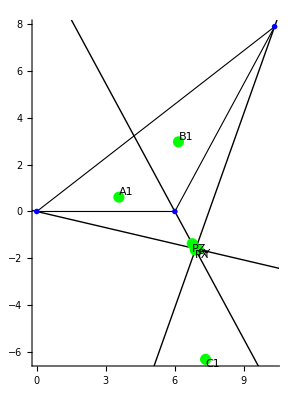

```mathematica
drawAubertLines[{XX,YY,ZZ},bKimberlingTriangle["4th Brocard"]]
```